Monte Carlo Simulation using Mathematica

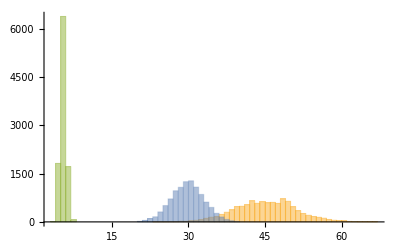

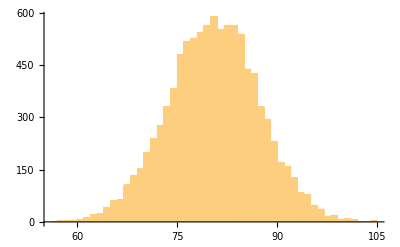

```mathematica
TempMean = 29.9;
TempStdDev = 3.2; 
LogMu = 1.7; 
LogSigma = 0.1; 
NoFanMean = 45;
NoFanStdDev=6;
FanMean=49; 
FanStdDev = 0.2;
SimulateNumber= 10000;
rnorms1= RandomVariate[TruncatedDistribution[{20,40},NormalDistribution[TempMean,TempStdDev]],SimulateNumber];
rnorms2= RandomVariate[LogNormalDistribution[LogMu,LogSigma],SimulateNumber];
rmix1 = RandomVariate[MixtureDistribution[{97,3},{NormalDistribution[NoFanMean,NoFanStdDev],NormalDistribution[FanMean,FanStdDev]}],SimulateNumber];
Temp1=rnorms1+rnorms2+rmix1;
Histogram[{rmix1, rnorms1,rnorms2},50]
Histogram[Temp1,50]
```